```mathematica
(*--- Biophysical model of inverse blebbing ---*)
(*--- Modified on 12/11/2021 ---*)
Clear[θ,solCC,solMM,eqsol];

SetDirectory["/Users/cairola/Dropbox (The Francis Crick)/ChiuFanShared/Project-Glaucoma/paper"];
date=DateString[{"Year","_","Month","_","Day"}];
If[DirectoryQ[date]==False,CreateDirectory[date]];
SetDirectory[date];
SetOptions[Style,FontFamily->"Arial"];

(*--- Plot Settings ---*)
Size=20;imgSize=600;imagePadding={{100,100},{80,10}};
dashsty=Directive[Dashed,AbsoluteThickness[1]];
mdefault=Directive[Black,AbsoluteThickness[2]];
cdefault=Directive[Darker[RGBColor[0,154,0,255]],AbsoluteThickness[2]];
bfont=Directive[Size,Black,FontFamily->"Arial"];
SetOptions[Plot,PlotRange->All];SetOptions[ListPlot,PlotRange->All,Joined->True];
SetOptions[ListLogPlot,PlotRange->All,Joined->True];
```

```mathematica
(*--- Numerical Algorithms ---*)
θ[y_]:={ArcSin[rm/y],π-ArcSin[rm/y]};
(*--- A. Vacuole: Cortex dominated phase ; Cell: Cortex dominated phase ---*)
solCC[p_,x0_]:=Module[{y,ϕ,k1,k2,rC,Γ0,Α0,Α,Σ0,S0,S,ΓV,ΓC,x1,x2,rV,rL,z,i,j,pC,counter,R},R={};
(*--- A.1 Set angle ---*)
For[j=1,j≤2,j++,
Clear[y,x1,x2,rV,rC,ΓV,ΓC,z];
(*--- A.2 Initialise parameters ---*)
k1=1;k2=1;counter=0;
ϕ=Part[θ[y],j];rC=(x0^3+2 y^3(2+Cos[ϕ])Sin[ϕ/2]^4)^(1/3);
Γ0=γM+ΤC;Α0=3π x0^2-π d^2;S0=π d^2;
Α=3π rC^2-π d^2;S=2π y^2(1-Cos[ϕ])+π (d^2-rm^2);
ΓV=Γ0;ΓC=Γ0;
(*--- A.3 Numerical solutions ---*)
rL=y/.NSolve[y^2+3(2 y^3+x0^3)^(2/3)==3 x0^2(1+αC)&&y>0,y];Clear[y];
x1=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k1 rL}]]]];Clear[y];
x2=Re[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k2 x0}]]];Clear[y];
(*--- A.3.1 Check solutions ---*)
While[Abs[x1-x2]<10^-2&&counter<10,k1/=10;counter+=1;
x1=First[Re[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k1 rL}]]]];Clear[y];
];
(*--- A.3.2 Set solutions ---*)
rV=Re[{x1,x2}];ϕ=Re[ϕ/.{y->rV}];
rC=Re[rC/.{y->rV}];
z=(2ΓC)/rC;
(*--- A.3.3 Check validity of numerical results ---*)
For[i=1,i<=Length[rV],i++,
(*Print[StringJoin["Check rV[[",ToString[i],"]]=",ToString[rV[[i]]]]];*)
If[rV[[i]]<0,rV=Drop[rV,{i}]; rC=Drop[rC,{i}]; z=Drop[z,{i}]; ϕ=Drop[ϕ,{i}]; i-=1,
pC=ΓC/rC[[i]]+ΓV/rV[[i]];
If[Abs[pC-p/2]>10^-2,
(*Print[StringJoin["pC=",ToString[ScientificForm[pC,2]]]];
Print[StringJoin["p/2=",ToString[ScientificForm[p/2,2]]]];
Print[StringJoin["ΔP=",ToString[ScientificForm[Abs[pC-p/2],2]]]];*)
rV=Drop[rV,{i}]; rC=Drop[rC,{i}];z=Drop[z,{i}]; ϕ=Drop[ϕ,{i}]; i-=1;
];
];
];
(*--- A.4 Print results ---*)
For[i=1,i<=Length[rV],i++,AppendTo[R,{rV[[i]],rC[[i]],z[[i]],ΓV,ΓC,ϕ[[i]]}]];
];
R=DeleteDuplicates[R,First@#1==First@#2 &];Return[R]
];
```

```mathematica
(*--- C. Vacuole: Membrane dominated phase ; Cell: Cortex dominated phase ---*)
solCM[p_,x0_]:=Module[{x1,x2,k1,k2,rV,rC,Σ0,σ0,ΓV,ΓC,y,z,rL,ϕ,pC,Α,Α0,ΑC,S,S0,SC,i,j,counter,R}, R={};
(*--- B.1 Set angle ---*)
For[j=1,j≤2,j++,
Clear[y,x1,x2,rV,rC,ΓV,ΓC,z];
(*--- B.2 Initialise parameters ---*)
k1=10;k2=1;counter=0;
ϕ=Part[θ[y],j];rC=(x0^3+2 y^3(2+Cos[ϕ])Sin[ϕ/2]^4)^(1/3);
Σ0=γM+ΤC;σ0=γM+ΤC;
Α0=3π x0^2-π d^2;S0=π d^2;
SC=S0(1+αC);
Α=3π rC^2-π d^2;S=2π y^2(1-Cos[ϕ])+π (d^2-rm^2);
ΓV=Σ0+b(Exp[(S-SC)/SC]-1);ΓC=σ0;
(*--- B.3 Numerical solutions ---*)
rL=y/.NSolve[y^2+3(2 y^3+x0^3)^(2/3)==3 x0^2(1+αC)&&y>0,y];Clear[y];
x1=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k1 rL}]]]];
x2=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k2 rL}]]]];
(*--- B.3.1 Check solutions ---*)
While[Abs[x1-x2]<10^-2&&counter<10,(*k1*=10;*)
k2/=10;counter+=1;
x2=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k2 rL}]]]];Clear[y];
];
(*--- B.3.2 Set solutions ---*)
rV=Sort[Re[{x1,x2}]];ϕ=Re[ϕ/.{y->rV}];
rC=Re[rC/.{y->rV}];
ΓV=Re[ΓV/.{y->rV}];z=(2ΓC)/rC;
(*--- B.3.3 Check validity of numerical results ---*)
For[i=1,i<=Length[rV],i++,
(*Print[StringJoin["Check rV[[",ToString[i],"]]=",ToString[rV[[i]]]]];*)
If[rV[[i]]<0,rV=Drop[rV,{i}]; rC=Drop[rC,{i}]; ΓV=Drop[ΓV,{i}]; z=Drop[z,{i}]; ϕ=Drop[ϕ,{i}]; i-=1,
pC=ΓC/rC[[i]]+ΓV[[i]]/rV[[i]];
If[Abs[pC-p/2]>10^-2,
(*Print[StringJoin["pC=",ToString[ScientificForm[pC,2]]]];
Print[StringJoin["p/2=",ToString[ScientificForm[p/2,2]]]];
Print[StringJoin["ΔP=",ToString[ScientificForm[Abs[pC-p/2],2]]]];*)
rV=Drop[rV,{i}];rC=Drop[rC,{i}];ΓV=Drop[ΓV,{i}];
z=Drop[z,{i}]; ϕ=Drop[ϕ,{i}]; i-=1;
];
];
];
(*--- B.4 Print results ---*)
For[i=1,i<=Length[rV],i++,AppendTo[R,{rV[[i]],rC[[i]],z[[i]],ΓV[[i]],ΓC,ϕ[[i]]}]];
];
R=DeleteDuplicates[R,First@#1==First@#2 &];
Return[R]
];
```

```mathematica
(*--- C. Vacuole: Membrane dominated phase ; Cell: Membrane dominated phase ---*)
solMM[p_,x0_]:=Module[{x1,x2,k1,k2,rV,rC,Σ0,σ0,ΓV,ΓC,y,z,rL,ϕ,pC,Α,Α0,ΑC,S,S0,SC,i,j,counter,R}, R={};
(*--- B.1 Set angle ---*)
For[j=1,j≤2,j++,
Clear[y,x1,x2,rV,rC,ΓV,ΓC,z];
(*--- B.2 Initialise parameters ---*)
k1=10;k2=1;counter=0;
ϕ=Part[θ[y],j];rC=(x0^3+2 y^3(2+Cos[ϕ])Sin[ϕ/2]^4)^(1/3);
Σ0=γM+ΤC;σ0=γM+ΤC;
Α0=3π x0^2-π d^2;S0=π d^2;
SC=S0(1+αC);ΑC=Α0(1+αC);
Α=3π rC^2-π d^2;S=2π y^2(1-Cos[ϕ])+π (d^2-rm^2);
ΓV=Σ0+b(Exp[(S-SC)/SC]-1);ΓC=σ0+b(Exp[(Α-ΑC)/ΑC]-1);
(*--- B.3 Numerical solutions ---*)
rL=y/.NSolve[y^2+3(2 y^3+x0^3)^(2/3)==3 x0^2(1+αC)&&y>0,y];Clear[y];
x1=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k1 rL}]]]];
x2=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k2 rL}]]]];
(*--- B.3.1 Check solutions ---*)
While[Abs[x1-x2]<10^-2&&counter<10,(*k1*=10;*)
k2/=10;counter+=1;
(*x1=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k1 rL}]]]];Clear[y];*)
x2=Re[First[y/.Quiet[FindRoot[ΓC/rC+ΓV/y==p/2,{y,k2 rL}]]]];Clear[y];
];
(*--- B.3.2 Set solutions ---*)
rV=Sort[Re[{x1,x2}]];ϕ=Re[ϕ/.{y->rV}];
rC=Re[rC/.{y->rV}]; ΓC=Re[ΓC/.{y->rV}];
ΓV=Re[ΓV/.{y->rV}];z=(2ΓC)/rC;
(*--- B.3.3 Check validity of numerical results ---*)
For[i=1,i<=Length[rV],i++,
(*Print[StringJoin["Check rV[[",ToString[i],"]]=",ToString[rV[[i]]]]];*)
If[rV[[i]]<0,rV=Drop[rV,{i}]; rC=Drop[rC,{i}]; ΓV=Drop[ΓV,{i}]; ΓC=Drop[ΓC,{i}]; z=Drop[z,{i}]; ϕ=Drop[ϕ,{i}]; i-=1,
pC=ΓC[[i]]/rC[[i]]+ΓV[[i]]/rV[[i]];
If[Abs[pC-p/2]>10^-2,
(*Print[StringJoin["pC=",ToString[ScientificForm[pC,2]]]];
Print[StringJoin["p/2=",ToString[ScientificForm[p/2,2]]]];
Print[StringJoin["ΔP=",ToString[ScientificForm[Abs[pC-p/2],2]]]];*)
rV=Drop[rV,{i}];rC=Drop[rC,{i}];ΓV=Drop[ΓV,{i}];
ΓC=Drop[ΓC,{i}];z=Drop[z,{i}]; ϕ=Drop[ϕ,{i}]; i-=1;
];
];
];
(*--- B.4 Print results ---*)
For[i=1,i<=Length[rV],i++,AppendTo[R,{rV[[i]],rC[[i]],z[[i]],ΓV[[i]],ΓC[[i]],ϕ[[i]]}]];
];
R=DeleteDuplicates[R,First@#1==First@#2 &];
Return[R]
];
```

```mathematica
(*--- C. Equilibrium solutions ---*)
eqsol[p_,x0_]:=Module[{s1,s2,s3,sF,Α,Α0,S,S0,rC,rV,r1,r2,r3,r4,xC,z,ϕ,i},sF={};
Α0=3π x0^2-π d^2;S0=π d^2;
(*--- A. ---*)
(*--- Vacuole: Cortex dominated phase ---*)
(*--- Cell: Cortex dominated phase ---*)
s1=solCC[p,x0];(*Print[s1];*)
For[i=1,i≤Length[s1],i++,
rV=Part[s1[[i]],1];rC=Part[s1[[i]],2]; ϕ=Part[s1[[i]],6];
Α=3π rC^2-π d^2;S=2π rV^2(1-Cos[ϕ])+π (d^2-rm^2);
If[Α≤Α0(1+αC)&&S≤S0(1+αC),AppendTo[sF,s1[[i]]];];
];
(*--- B. ---*)
(*--- Vacuole: Membrane dominated phase ---*)
(*--- Cell: Cortex dominated phase ---*)
s2=solCM[p,x0];(*Print[s2];*)
For[i=1,i≤Length[s2],i++,
rV=Part[s2[[i]],1];rC=Part[s2[[i]],2]; ϕ=Part[s2[[i]],6];
Α=3π rC^2-π d^2;S=2π rV^2(1-Cos[ϕ])+π (d^2-rm^2);
If[ S≥S0(1+αC)&&Α≤Α0(1+αC),AppendTo[sF,s2[[i]]];];
];
(*--- C. ---*)
(*--- Vacuole: Membrane dominated phase ---*)
(*--- Cell: Membrane dominated phase ---*)
s3=solMM[p,x0];(*Print[s2];*)
For[i=1,i≤Length[s3],i++,
rV=Part[s3[[i]],1];rC=Part[s3[[i]],2]; ϕ=Part[s3[[i]],6];
Α=3π rC^2-π d^2;S=2π rV^2(1-Cos[ϕ])+π (d^2-rm^2);
If[ S≥S0(1+αC)&&Α≥Α0(1+αC),AppendTo[sF,s3[[i]]];];
];
(*--- Final solution ---*)
sF=Select[sF,Length[#]==6&];
Return[sF];
];
```

```mathematica
solMM[20,10]
```

{{1.00166,10.0067,-630.214,325.645,-3153.18,2.88934}}

```mathematica
(*--- Generate phase-diagram ---*)
Clear[γM,ΤC,r0,rm,αC,b,ΔΑ,PlysV,PlysC,p1,ρ,pdiag];
indx=1; fstream=OpenWrite[StringJoin[Directory[],"/dataset_",ToString[indx],".txt"]];
(*--- 1. Membrane surface tension (pN/μm) ---*)
γM=40;Export[fstream,StringJoin["γM=",ToString[γM],"\n"]];
(*--- 2 Cell cortex surface tension (rest state) (pN/μm) ---*)
ΤC=374;Export[fstream,StringJoin["ΤC=",ToString[ΤC],"\n"]];
(*--- 3. Initial cell radius (μm) ---*)
(*--- Realistic values: 9-11 μm ---*)
r0=10;Export[fstream,StringJoin["r0=",ToString[r0],"\n"]];
(*--- 5. Pore radius (μm) ---*)
(*--- Realistic values: 1-4 μm ---*)
rm=0.25;Export[fstream,StringJoin["rm=",ToString[rm],"\n"]];
(*--- 6. Membrane patch (μm) ---*)
(*--- Realistic values: 10 μm ---*)
d=10.;Export[fstream,StringJoin["d=",ToString[d],"\n"]];
(*--- 6. Reservoir size ---*)
(*--- Realistic values: 0%-1000%  ---*)
αC=0.5;Export[fstream,StringJoin["αC=",ToString[αC],"\n"]];
ΔΑ=αC;(*Export[fstream,StringJoin["ΔΑ=",ToString[ΔΑ],"\n"]];*)
(*--- 7. Stretching strength ---*)
(*--- Realistic values: (0.08-2)10^5 pN/μm ---*)
b=1.0 10^5;Export[fstream,StringJoin["b=",ToString[b],"\n"]];
(*--- 8. Conversion factor Pa -> μm ---*)
cf=0.0075;
(*--- 9. Maximal membrane stretching ---*)
(*--- Realistic values: 2-5% ---*)
αl=0.05;sC=(π d^2)(1+αC); sM=(1+αl)sC;PlysV=γM+ΤC+b(Exp[(sM-sC)/sC]-1); (*PlysV=γM+ΤC+Δσ+b(Abs[(sM-sC)/sC])^β;*)
aC=(3π r0^2-π d^2)(1+αC); aM=(1+αl)aC;PlysC=γM+ΤC+b(Exp[(aM-aC)/aC]-1);(* PlysC=γM+ΤC+Δσ+b(Abs[(aM-aC)/aC])^β;*)
Close[fstream];


logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
p1=0.1;p2=4000;P=5000;
ρ=logspace[Log10[p1],Log10[p2],P];
p1=cf;p2=4000 cf;
SetSharedVariable[j];
pdiag=Monitor[ParallelTable[j=Length[ρ]-n;{ρ[[n]],eqsol[ρ[[n]],r0]},{n,1,Length[ρ]}],j];
Export[StringJoin["pdiag_c_",ToString[indx],".txt"],pdiag,"Table"];
```

```mathematica
(*--- Figures ---*)
(*--- Subdivide the table of results ---*)
Print["Check the table of results:"];
T0=Select[pdiag,Length[Part[#,2]]==0&];
T1=Select[pdiag,Length[Part[#,2]]==1&];Print["Length T1=",Length[T1]];
T1row=T1[[All,1]];T1col=Flatten[T1[[All,2]],1];
T2=Select[pdiag,Length[Part[#,2]]==2&];Print["Length T2=",Length[T2]];
T2row=T2[[All,1]];T2col=T2[[All,2]];
T3=Select[pdiag,Length[Part[#,2]]==3&];Print["Length T3=",Length[T3]];
T3row=T3[[All,1]];T3col=T3[[All,2]];
T4=Select[pdiag,Length[Part[#,2]]==4&];Print["Length T4=",Length[T4]];
T4row=T4[[All,1]];T4col=T4[[All,2]];
T5=Select[pdiag,Length[Part[#,2]]==5&];Print["Length T5=",Length[T5]];
T5row=T5[[All,1]];T5col=T5[[All,2]];
```

Check the table of results:

Length T1=625

Length T2=5

Length T3=1122

Length T4=78

Length T5=0

```mathematica
(*--- Manage data ---*)
dat1=Table[{T1row[[n]] cf,T1col[[n,1]],T1col[[n,2]],T1col[[n,3]]cf,T1col[[n,4]],T1col[[n,5]],T1col[[n,6]]},{n,1,Length[T1row]}];
dat2=Table[{T2row[[n]] cf,T2col[[n,m,1]],T2col[[n,m,2]],T2col[[n,m,3]]cf,T2col[[n,m,4]],T2col[[n,m,5]],T2col[[n,m,6]]},{n,1,Length[T2row]},{m,1,2}];
dat3=Table[{T3row[[n]] cf,T3col[[n,m,1]],T3col[[n,m,2]],T3col[[n,m,3]]cf,T3col[[n,m,4]],T3col[[n,m,5]],T3col[[n,m,6]]},{n,1,Length[T3row]},{m,1,3}];
dat4=Table[{T4row[[n]] cf,T4col[[n,m,1]],T4col[[n,m,2]],T4col[[n,m,3]]cf,T4col[[n,m,4]],T4col[[n,m,5]],T4col[[n,m,6]]},{n,1,Length[T4row]},{m,1,4}];

(*--- Rearrange data to make plots ---*)
(*--- Vacuole ---*)
areaV[r_,ϕ_]:=2π r^2(1-Cos[ϕ])+π (d^2-rm^2);
s0=π d^2;

areaC[R_]:=3π R^2-π d^2;
a0=3π r0^2-π d^2;

Tdat1=Select[dat1, Part[#,5]>PlysV&];
Mdat1=Select[dat1,areaV[Part[#,2],Part[#,7]]≥s0(1+αC) && Part[#,5]<=PlysV&];
Cdat1=Select[dat1, Part[#,2]≥rm && Part[#,7]≥π/2 && areaV[Part[#,2],Part[#,7]]≤s0(1+αC) &];

Tdat2=Select[Flatten[dat2,1], Part[#,5]>PlysV&];
Mdat2=Select[Flatten[dat2,1], areaV[Part[#,2],Part[#,7]]≥s0(1+αC) && Part[#,5]<=PlysV &];
Cdat2=Select[Flatten[dat2,1], Part[#,2]≥rm && Part[#,7]≥π/2 &&areaV[Part[#,2],Part[#,7]]≤s0(1+αC)  &];

Tdat3=Select[Flatten[dat3,1], Part[#,5]>PlysV&];
Mdat3=Select[Flatten[dat3,1], areaV[Part[#,2],Part[#,7]]≥s0(1+αC) && Part[#,5]<=PlysV &];
Cdat3=Select[Flatten[dat3,1], Part[#,2]≥rm && Part[#,7]≥π/2 &&areaV[Part[#,2],Part[#,7]]≤s0(1+αC) &];

Tdat4=Select[Flatten[dat4,1], Part[#,5]>PlysV&];
Mdat4=Select[Flatten[dat4,1], areaV[Part[#,2],Part[#,7]]≥s0(1+αC) && Part[#,5]<=PlysV &];
Cdat4=Select[Flatten[dat4,1], Part[#,2]≥rm && Part[#,7]≥π/2&& areaV[Part[#,2],Part[#,7]]≤s0(1+αC) &];

Cdat=Join[Cdat1,Cdat2,Cdat3,Cdat4];
rVCdat=Cdat[[;;,1;;2]]; ΓVCdat=Cdat[[;;,1;;5;;4]]; ϕCdat=Cdat[[;;,1;;7;;6]];PCCdat=Cdat[[;;,1;;4;;3]];
rCCdat=Cdat[[;;,1;;3;;2]];ΓCCdat=Cdat[[;;,1;;6;;5]];

Mdat=Join[Mdat1,Mdat2,Mdat3,Mdat4];
rVMdat=Mdat[[;;,1;;2]];ΓVMdat=Mdat[[;;,1;;5;;4]];ϕMdat=Mdat[[;;,1;;7;;6]];PCMdat=Mdat[[;;,1;;4;;3]];
rCMdat=Mdat[[;;,1;;3;;2]];ΓCMdat=Mdat[[;;,1;;6;;5]]; 

Tdat=Join[Tdat1,Tdat2,Tdat3,Tdat4];
rVTdat=Tdat[[;;,1;;2]]; PCTdat=Tdat[[;;,1;;4;;3]];ΓVTdat=Tdat[[;;,1;;5;;4]];ϕTdat=Tdat[[;;,1;;7;;6]];


(*--- Cell ---*)
areaC[R_]:=3π R^2-π d^2;
a0=3π r0^2-π d^2;

Tdat1=Select[dat1, Part[#,6]>PlysC&];
Mdat1=Select[dat1,areaC[Part[#,3]]≥a0(1+αC) && Part[#,6]<=PlysC&];
Cdat1=Select[dat1, Part[#,2]≥rm && Part[#,7]≥π/2 &&  areaC[Part[#,3]]≤a0(1+αC) &];

Tdat2=Select[Flatten[dat2,1], Part[#,6]>PlysC&];
Mdat2=Select[Flatten[dat2,1], areaC[Part[#,3]]≥a0(1+αC) && Part[#,6]<=PlysC &];
Cdat2=Select[Flatten[dat2,1], Part[#,2]≥rm && Part[#,7]≥π/2 &&areaC[Part[#,3]]≤a0(1+αC)  &];

Tdat3=Select[Flatten[dat3,1], Part[#,6]>PlysC&];
Mdat3=Select[Flatten[dat3,1], areaC[Part[#,3]]≥a0(1+αC) && Part[#,6]<=PlysC &];
Cdat3=Select[Flatten[dat3,1], Part[#,2]≥rm && Part[#,7]≥π/2 &&areaC[Part[#,3]]≤a0(1+αC) &];

Tdat4=Select[Flatten[dat4,1], Part[#,6]>PlysC&];
Mdat4=Select[Flatten[dat4,1], areaC[Part[#,3]]≥a0(1+αC) && Part[#,6]<=PlysC &];
Cdat4=Select[Flatten[dat4,1], Part[#,2]≥rm && Part[#,7]≥π/2 && areaC[Part[#,3]]≤a0(1+αC) &];

Cdat=Join[Cdat1,Cdat2,Cdat3,Cdat4];
rCCdat=Cdat[[;;,1;;3;;2]];ΓCCdat=Cdat[[;;,1;;6;;5]];

Mdat=Join[Mdat1,Mdat2,Mdat3,Mdat4];
rCMdat=Mdat[[;;,1;;3;;2]];ΓCMdat=Mdat[[;;,1;;6;;5]]; 

Tdat=Join[Tdat1,Tdat2,Tdat3,Tdat4];
rCTdat=Tdat[[;;,1;;3;;2]];ΓCTdat=Tdat[[;;,1;;6;;5]];
```

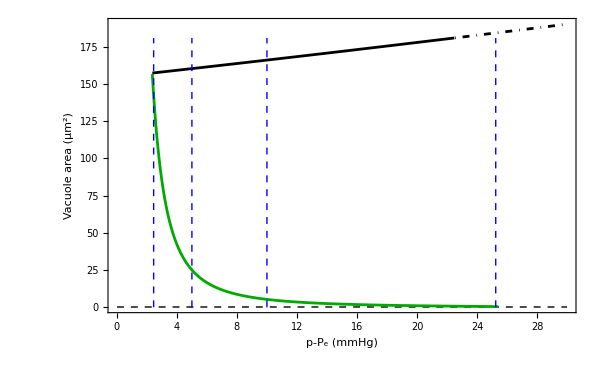

```mathematica
(*--- Data analysis ---*)
(*--- 1.1 Vacuole area vs p-Subscript[P, e] ---*)
Av[x_,ϕ_]:=Module[{z},
z=2π x^2(1-Cos[ϕ]);
Return[z];
]
(*--- Vacuole total area---*)
Av1=ParallelTable[{rVCdat[[n,1]],Av[rVCdat[[n,2]],ϕCdat[[n,2]]]},{n,1,Length[rVCdat]}];
Av1=Sort[Av1,#1[[2]]<#2[[2]]&]; 
Av2=ParallelTable[{rVMdat[[n,1]],Av[rVMdat[[n,2]],ϕMdat[[n,2]]]},{n,1,Length[rVMdat]}];
Av2=Sort[Av2,#1[[2]]<#2[[2]]&]; 
Av3=ParallelTable[{rVTdat[[n,1]],Av[rVTdat[[n,2]],ϕTdat[[n,2]]]},{n,1,Length[rVTdat]}];
Av3=Sort[Av3,#1[[2]]<#2[[2]]&]; 

c1=2.45;c2=5;c3=10;c4=25.25;
line1=Line[{{c1 ,0},{c1,Max[Av2]}}];
line2=Line[{{c2 ,0},{c2,Max[Av2]}}];
line3=Line[{{c3 ,0},{c3,Max[Av2]}}];
line4=Line[{{c4 ,0},{c4,Max[Av2]}}];

f1a=Show[Plot[π rm^2,{x,p1,p2},PlotStyle->{Black,dashsty}],
ListPlot[Av1,PlotStyle->cdefault],
ListPlot[Av2,PlotStyle->mdefault],
ListPlot[Av3,PlotStyle->{DotDashed,mdefault}],
Epilog->{Directive[Blue,dashsty],line1,line2,line3,line4},
PlotRange->{{p1,p2},All},Frame->True,BaseStyle->bfont,
FrameTicks->{Automatic,Automatic},FrameTicksStyle->{Automatic,Automatic},
FrameLabel->{Style["p-P_e (mmHg)",bfont],Style["Vacuole area (μm^2)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
fname1a=StringJoin["Av_",ToString[indx],".pdf"];
Export[fname1a,f1a];
```

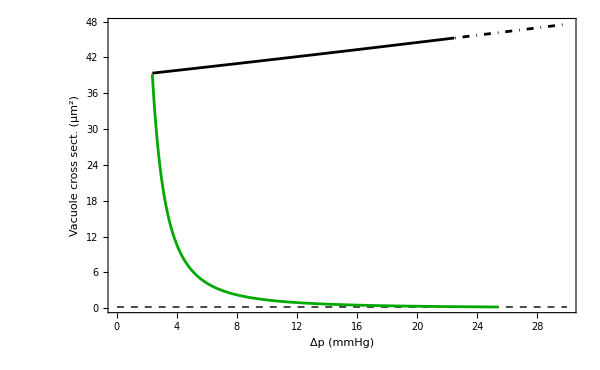

```mathematica
(*--- 1.2 Cross section vs p-Subscript[P, e] ---*)
csect[x_,ϕ_]:=Module[{z},
If[ϕ≥π/2,z=π x^2,z=π rm^2];
Return[z];
]
(*--- Vacuole total area---*)
S1=ParallelTable[{rVCdat[[n,1]],csect[rVCdat[[n,2]],ϕCdat[[n,2]]]},{n,1,Length[rVCdat]}];
S1=Sort[S1,#1[[2]]<#2[[2]]&]; 
S2=ParallelTable[{rVMdat[[n,1]],csect[rVMdat[[n,2]],ϕMdat[[n,2]]]},{n,1,Length[rVMdat]}];
S2=Sort[S2,#1[[2]]<#2[[2]]&]; 
S3=ParallelTable[{rVTdat[[n,1]],csect[rVTdat[[n,2]],ϕTdat[[n,2]]]},{n,1,Length[rVTdat]}];
S3=Sort[S3,#1[[2]]<#2[[2]]&]; 

f1c=Show[Plot[π rm^2,{x,p1,p2},PlotStyle->{Black,dashsty}],
ListPlot[S1,PlotStyle->cdefault],
ListPlot[S2,PlotStyle->mdefault],
ListPlot[S3,PlotStyle->{DotDashed,mdefault}],
PlotRange->{{p1,p2},All},Frame->True,BaseStyle->bfont,
FrameTicks->{Automatic,Automatic},FrameTicksStyle->{Automatic,Automatic},
FrameLabel->{Style["Δp (mmHg)",bfont],Style["Vacuole cross sect. (μm^2)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
fname1c=StringJoin["csect_",ToString[indx],".pdf"];
Export[fname1c,f1c];
```

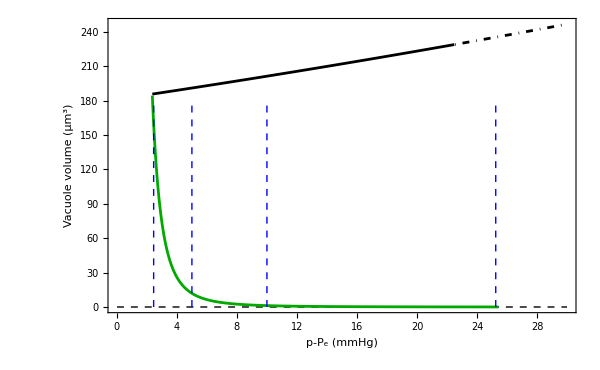

```mathematica
(*--- 1.3 Vacuole volume vs p-Subscript[P, e] ---*)
VacV[x_,ϕ_]:=Module[{z},
z=4/3 π x^3(2+Cos[ϕ])(Sin[ϕ/2])^4;
Return[z];
]
(*--- Vacuole total area---*)
Vv1=ParallelTable[{rVCdat[[n,1]],VacV[rVCdat[[n,2]],ϕCdat[[n,2]]]},{n,1,Length[rVCdat]}];
Vv1=Sort[Vv1,#1[[2]]<#2[[2]]&]; 
Vv2=ParallelTable[{rVMdat[[n,1]],VacV[rVMdat[[n,2]],ϕMdat[[n,2]]]},{n,1,Length[rVMdat]}];
Vv2=Sort[Vv2,#1[[2]]<#2[[2]]&]; 
Vv3=ParallelTable[{rVTdat[[n,1]],VacV[rVTdat[[n,2]],ϕTdat[[n,2]]]},{n,1,Length[rVTdat]}];
Vv3=Sort[Vv3,#1[[2]]<#2[[2]]&]; 

f1c=Show[Plot[0,{x,p1,p2},PlotStyle->{Black,dashsty}],
ListPlot[Vv1,PlotStyle->cdefault],
ListPlot[Vv2,PlotStyle->mdefault],
ListPlot[Vv3,PlotStyle->{DotDashed,mdefault}],
Epilog->{Directive[Blue,dashsty],line1,line2,line3,line4},
PlotRange->{{p1,p2},All},Frame->True,BaseStyle->bfont,
FrameTicks->{Automatic,Automatic},FrameTicksStyle->{Automatic,Automatic},
FrameLabel->{Style["p-P_e (mmHg)",bfont],Style["Vacuole volume (μm^3)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
fname1c=StringJoin["Volume_",ToString[indx],".pdf"];
Export[fname1c,f1c];
```

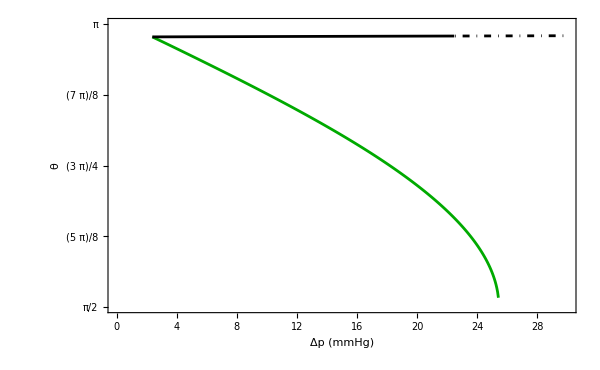

```mathematica
(*--- 1.c Phase diagram: θ vs p-Subscript[P, e] ---*)
ϕ1=Sort[ϕCdat,#1[[2]]<#2[[2]]&]; 
ϕ2=Sort[ϕMdat,#1[[2]]<#2[[2]]&]; 
ϕ3=Sort[ϕTdat,#1[[2]]<#2[[2]]&]; 
f1b=Show[
ListPlot[ϕ1,PlotStyle->cdefault],
ListPlot[ϕ2,PlotStyle->mdefault],
ListPlot[ϕ3,PlotStyle->{DotDashed,mdefault}],
PlotRange->{{p1,p2},{Pi/2,Pi}},Frame->True,BaseStyle->bfont,
FrameTicks->{{{π/2,5π/8,3π/4,7π/8,π},{π/2,5π/8,3π/4,7π/8,π}},{Automatic,Automatic}},FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Directive[FontOpacity->0,FontSize->0]}},
FrameLabel->{Style["Δp (mmHg)",bfont],Style["θ",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
fname1b=StringJoin["θ_",ToString[indx],".pdf"];
Export[fname1b,f1b];
```

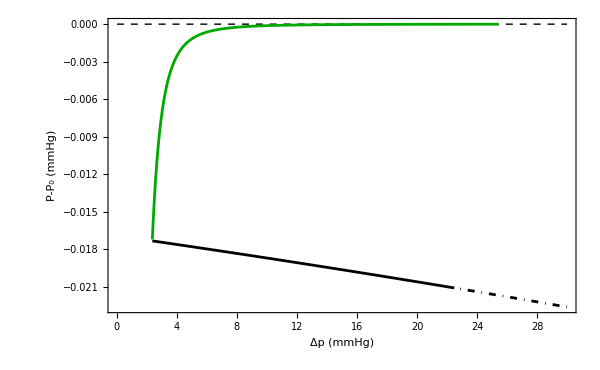

```mathematica
(*--- 2. P-Subscript[P, e] vs p-Subscript[P, e] ---*)
P1=Sort[PCCdat,#1[[2]]<#2[[2]]&];
P1=Table[{P1[[n,1]],P1[[n,2]]-(2(γM+ΤC)/r0)cf},{n,1,Length[P1]}]; 
P2=Sort[PCMdat,#1[[2]]<#2[[2]]&]; 
P2=Table[{P2[[n,1]],P2[[n,2]]-(2(γM+ΤC)/r0)cf},{n,1,Length[P2]}]; 
P3=Sort[PCTdat,#1[[2]]<#2[[2]]&]; 
P3=Table[{P3[[n,1]],P3[[n,2]]-(2(γM+ΤC)/r0)cf},{n,1,Length[P3]}]; 
f2=Show[Plot[0,{x,p1,p2},PlotRange->All,PlotStyle->{Black,dashsty}],
ListPlot[P3,PlotStyle->{DotDashed,mdefault}],
ListPlot[P2,PlotStyle->mdefault],
ListPlot[P1,PlotStyle->cdefault],
Frame->True,BaseStyle->bfont,FrameLabel->{Style["Δp (mmHg)",bfont],Style["P-P_0 (mmHg)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
fname2=StringJoin["Pcres_",ToString[indx],".pdf"];
Export[fname2,f2];
```

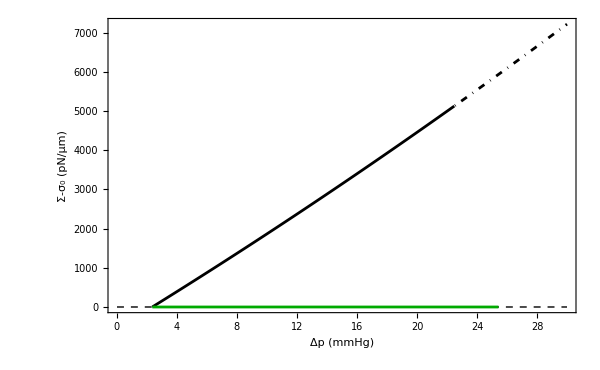

```mathematica
(*--- 3. Σ vs p-Subscript[P, e] ---*)
Γ1=ParallelTable[{ΓVCdat[[n,1]],ΓVCdat[[n,2]]-(γM+ΤC)},{n,1,Length[rVCdat]}];
Γ1=Sort[Γ1,#1[[2]]<#2[[2]]&]; 
Γ2=ParallelTable[{ΓVMdat[[n,1]],ΓVMdat[[n,2]]-(γM+ΤC)},{n,1,Length[rVMdat]}];
Γ2=Sort[Γ2,#1[[2]]<#2[[2]]&]; 
Γ3=ParallelTable[{ΓVTdat[[n,1]],ΓVTdat[[n,2]]-(γM+ΤC)},{n,1,Length[rVTdat]}];
Γ3=Sort[Γ3,#1[[2]]<#2[[2]]&]; 
f3=Show[Plot[0,{x,p1,p2},PlotStyle->{Black,dashsty}],
ListPlot[Γ3,PlotStyle->{DotDashed,mdefault}],
ListPlot[Γ2,PlotStyle->mdefault],
ListPlot[Γ1,PlotStyle->cdefault],PlotRange->{All,All},
Frame->True,BaseStyle->bfont,FrameLabel->{Style["Δp (mmHg)",bfont],Style["Σ-σ_0 (pN/μm)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
fname3=StringJoin["Gres_",ToString[indx],".pdf"];
Export[fname3,f3];
```

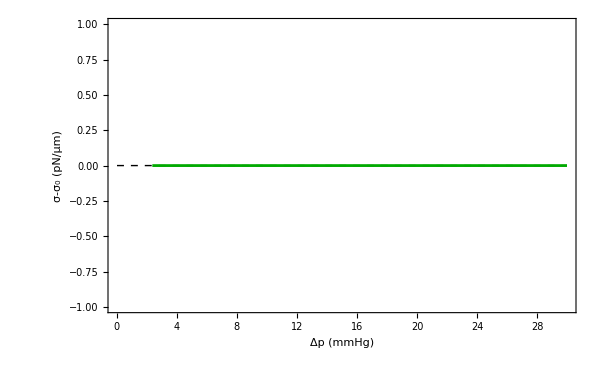

```mathematica
(*--- 3. σ vs p-Subscript[P, e] ---*)
Γ1=ParallelTable[{ΓCCdat[[n,1]],ΓCCdat[[n,2]]-(γM+ΤC)},{n,1,Length[rCCdat]}];
Γ1=Sort[Γ1,#1[[2]]<#2[[2]]&]; 
Γ2=ParallelTable[{ΓCMdat[[n,1]],ΓCMdat[[n,2]]-(γM+ΤC)},{n,1,Length[rCMdat]}];
Γ2=Sort[Γ2,#1[[2]]<#2[[2]]&]; 
Γ3=ParallelTable[{ΓCTdat[[n,1]],ΓCTdat[[n,2]]-(γM+ΤC)},{n,1,Length[rCTdat]}];
Γ3=Sort[Γ3,#1[[2]]<#2[[2]]&]; 
f4=Show[Plot[0,{x,p1,p2},PlotStyle->{Black,dashsty}],
ListPlot[Γ3,PlotStyle->{DotDashed,mdefault}],
ListPlot[Γ2,PlotStyle->mdefault],
ListPlot[Γ1,PlotStyle->cdefault],PlotRange->{All,All},
Frame->True,BaseStyle->bfont,FrameLabel->{Style["Δp (mmHg)",bfont],Style["σ-σ_0 (pN/μm)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
fname4=StringJoin["sigmaC_",ToString[indx],".pdf"];
Export[fname4,f4];
```

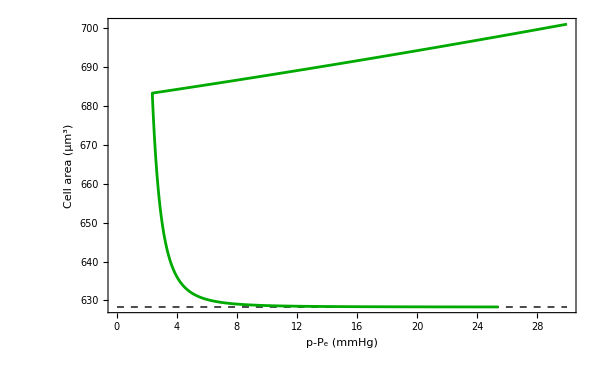

```mathematica
(*--- 1.3 Cell area vs p-Subscript[P, e] ---*)
CellA[x_]:=Module[{z},
z=3π x^2-π d^2;
Return[z];
]

CΑ1=ParallelTable[{rCCdat[[n,1]],CellA[rCCdat[[n,2]]]},{n,1,Length[rCCdat]}];
CΑ1=Sort[CΑ1,#1[[2]]<#2[[2]]&];
CΑ2=ParallelTable[{rCMdat[[n,1]],CellA[rCMdat[[n,2]]]},{n,1,Length[rCMdat]}];
CΑ2=Sort[CΑ2,#1[[2]]<#2[[2]]&]; 
CΑ3=ParallelTable[{rCTdat[[n,1]],CellA[rCTdat[[n,2]]]},{n,1,Length[rCTdat]}];
CΑ3=Sort[CΑ3,#1[[2]]<#2[[2]]&]; 

f5=Show[Plot[a0,{x,p1,p2},PlotStyle->{Black,dashsty}],
ListPlot[CΑ1,PlotStyle->cdefault],
(*ListPlot[CΑ2,PlotStyle->mdefault],
ListPlot[CΑ3,PlotStyle->{DotDashed,mdefault}],*)
PlotRange->{{p1,p2},{a0,Max[CΑ1]}},Frame->True,BaseStyle->bfont,
FrameTicks->{Automatic,Automatic},FrameTicksStyle->{Automatic,Automatic},
FrameLabel->{Style["p-P_e (mmHg)",bfont],Style["Cell area (μm^3)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
fname5=StringJoin["CellArea_",ToString[indx],".pdf"];
Export[fname5,f5];
```

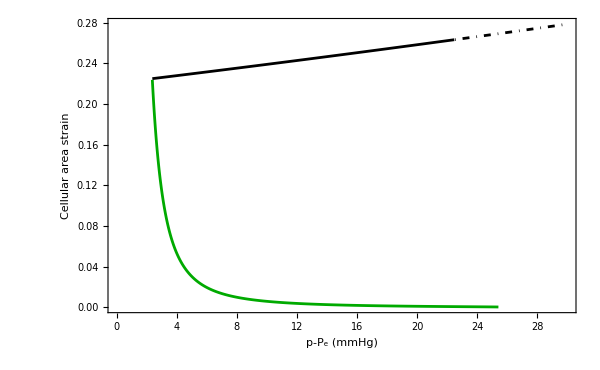

```mathematica
(*--- 1.4 Total area strain vs p-Subscript[P, e] ---*)
strain1=ParallelTable[{Av1[[n,1]],(-1+(Av1[[n,2]]+CΑ1[[n,2]]-π rm^2)/(3π r0^2))},{n,1,Length[Av1]}];
strain2=ParallelTable[{Av2[[n,1]],(-1+(Av2[[n,2]]+CΑ1[[n+Length[Av1],2]]-π rm^2)/(3π r0^2))},{n,1,Length[Av2]}];
strain3=ParallelTable[{Av3[[n,1]],(-1+(Av3[[n,2]]+CΑ1[[n+Length[Av1]+Length[Av2],2]]-π rm^2)/(3π r0^2))},{n,1,Length[Av3]}];

f6=Show[
ListPlot[strain1,PlotStyle->cdefault],
ListPlot[strain2,PlotStyle->mdefault],
ListPlot[strain3,PlotStyle->{DotDashed,mdefault}],
PlotRange->{{p1,p2},All},Frame->True,BaseStyle->bfont,
FrameTicks->{Automatic,Automatic},FrameTicksStyle->{Automatic,Automatic},
FrameLabel->{Style["p-P_e (mmHg)",bfont],Style["Cellular area strain",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
fname6=StringJoin["AreaStrain_",ToString[indx],".pdf"];
Export[fname6,f6];
```

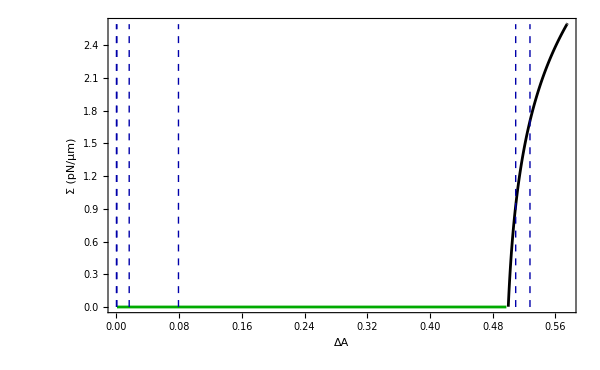

```mathematica
(*--- 4. σ vs Α ---*)
A1=ParallelTable[{(-s0+areaV[rVCdat[[n,2]],ϕCdat[[n,2]]])/s0,Log[ΓVCdat[[n,2]]/(γM+ΤC)]},{n,1,Length[rVCdat]}];
A1=Sort[A1,#1[[1]]<#2[[1]]&]; 
A2=ParallelTable[{(-s0+areaV[rVMdat[[n,2]],ϕMdat[[n,2]]])/s0,Log[ΓVMdat[[n,2]]/(γM+ΤC)]},{n,1,Length[rVMdat]}];
A2=Sort[A2,#1[[1]]<#2[[1]]&]; 
A3=ParallelTable[{(-s0+areaV[rVTdat[[n,2]],ϕTdat[[n,2]]])/s0,Log[ΓVTdat[[n,2]]/(γM+ΤC)]},{n,1,Length[rVTdat]}];
A3=Sort[A3,#1[[1]]<#2[[1]]&]; 
(*maxA=Log[Max[A3[[;;,1]]]];minA=Log[Min[A1[[;;,1]]]];*)
γmax=Max[A2[[;;,2]]];γmin=0;
maxA=Max[A2[[;;,1]]];minA=Min[A1[[;;,1]]];
(*γmax=Max[A3[[;;,2]]];γmin=0;*)
xtick=Range[0,maxA,500];

(*Point 1*)
s1=eqsol[c1/cf,r0];
κ=Part[s1,1,1]; ψ=Part[s1,1,6];
P1=(-s0+areaV[κ,ψ])/s0;
(*Point 2*)
s4=eqsol[c4/cf,r0]; 
κ=Part[s4,1,1]; ψ=Part[s4,1,6];
P2=(-s0+areaV[κ,ψ])/s0;
(*Points 3*)
s2=eqsol[c3/cf,r0]; 
κ=Part[s2,2,1]; ψ=Part[s2,2,6];
P3=(-s0+areaV[κ,ψ])/s0;
(*Points 4, 5*)
s3=eqsol[c2/cf,r0]; 
κ=Part[s3,2,1]; ψ=Part[s3,2,6];
P4=(-s0+areaV[κ,ψ])/s0;
κ=Part[s3,3,1]; ψ=Part[s3,3,6];
P5=(-s0+areaV[κ,ψ])/s0;
(*Point 6*)
s6=eqsol[c3/cf,r0];
κ=Part[s6,3,1]; ψ=Part[s6,3,6];
P6=(-s0+areaV[κ,ψ])/s0;

line1=Line[{{P1 ,0},{P1,γmax}}];
line2=Line[{{P2 ,0},{P2,γmax}}];
line3=Line[{{P3 ,0},{P3,γmax}}];
line4=Line[{{P4 ,0},{P4,γmax}}];
line5=Line[{{P5 ,0},{P5,γmax}}];
line6=Line[{{P6 ,0},{P6,γmax}}];
(*line7=Line[{{minA ,Log[γM+ΤC]},{maxA,Log[γM+ΤC]}}];*)

f4=Show[
ListPlot[A1,PlotStyle->cdefault,Joined->True],
ListPlot[A2,PlotStyle->mdefault,Joined->True],
ListPlot[A3,PlotStyle->{DotDashed,mdefault},Joined->True],
Epilog->{{Directive[Darker[Blue],dashsty],line1,line2,line3,line4,line5,line6}},
PlotRange->{{minA,maxA},{γmin,γmax}},Frame->True,BaseStyle->bfont,FrameTicksStyle->{{bfont,Directive[FontOpacity->0,FontSize->0]},{bfont,Directive[FontOpacity->0,FontSize->0]}},FrameLabel->{Style["ΔA",bfont],Style["Σ (pN/μm)",bfont]},
FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
fname4=StringJoin["Ares_",ToString[indx],".pdf"];
Export[fname4,f4];
```

{{1.70451,25.0002,33.133,414.,0.823237}}

{{1.70451,25.0002,33.133,414.,0.823237},{8.7299,25.3499,33.2364,2119.99,2.99791}}

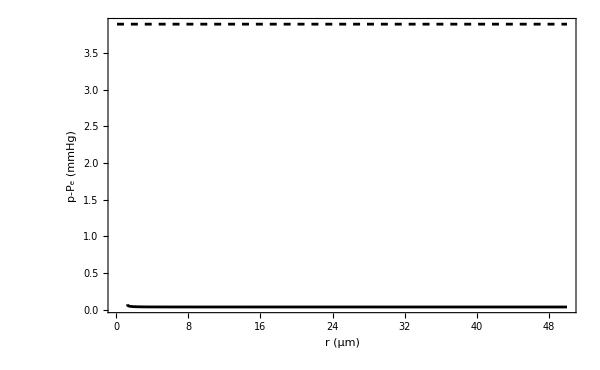

```mathematica
(*--- Appendix A: Numerical check ---*)
lhs[y_,x0_]:=Module[{rV,rC,σ0,Σ0,ΓV,ΓC,z,ϕ,Α,Α0,ΑC,S,S0,SC},
σ0=γM+ΤC;Σ0=γM+ΤC;
(*σ0=γM+ΤC+Δσ;Σ0=γM+ΤC+Δσ;*)
Α0=4π x0^2-π rE^2;ΑC=Α0(1+αC);
S0=π rE^2;SC=S0(1+αC);
ϕ=Part[θ[y],1];
rC=(x0^3+y^3(2+Cos[ϕ])Sin[ϕ/2]^4)^(1/3);
Α=4π rC^2-π rE^2;S=2π y^2(1-Cos[ϕ]);
ΓV=Σ0+Δσ/ΔΑ(S/S0-1)^α;
ΓC=σ0+Δσ/ΔΑ(Α/Α0-1)^α;
(*ΓV=Σ0+b(Exp[c(S-SC)/SC]-1);*)
(*ΓC=σ0+b( Exp[c(Α-ΑC)/ΑC]-1);*)
z=(2ΓC)/rC+(2ΓV)/y;
Return[S]
];

x1=3.891906796828176/cf;(*x2=4/cf;x3=6/cf;*)
Print[solCC[x1,r0]];(*Print[solMC[x2,r0]];Print[solMC[x3,r0]];*)
Print[eqsol[x1,r0]];(*Print[eqsol[x2,r0]];Print[eqsol[x3,r0]];*)
Show[Plot[lhs[y,r0]cf,{y,rm,50},PlotStyle->{AbsoluteThickness[2],Black}],Plot[x1 cf,{y,0.1,50},PlotStyle->{Dashed,AbsoluteThickness[2],Black}],
(*Plot[x2 cf,{y,0.1,50},PlotStyle->{Dashed,AbsoluteThickness[2],Red}],
Plot[x3 cf,{y,0.1,50},PlotStyle->{Dashed,AbsoluteThickness[2],Green}],*)
PlotRange->{All,All},Frame->True,BaseStyle->{FontSize->Size},FrameStyle->{{Black,FontSize->Size},{Black,FontSize->Size}},FrameLabel->{Style["r (μm)",Size],Style["p-P_e (mmHg)",Size]},ImageSize->imgSize,ImagePadding->imagePadding]
```

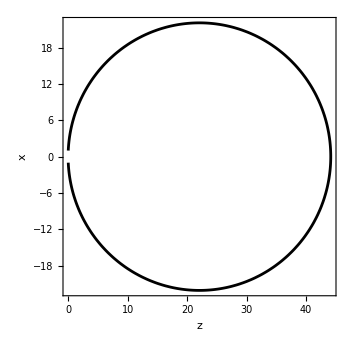

```mathematica
(*--- Plot of inverse blebs ---*)
Size=20;imgSize=350;imagePadding={{80,50},{50,2}};
(*--- Vacuole radius rescaled with respect to rm ---*)
x[r_,ψ_,ϕ_]:=r Cos[ψ]Sin[θ[r rm]-ϕ];
y[r_,ψ_,ϕ_]:=r Sin[ψ]Sin[θ[r rm]-ϕ];
z[r_,ϕ_]:=r Cos[θ[r rm]-ϕ]-r Cos[θ[r rm]];
(*f1=Show[ParametricPlot3D[{x[θ,s],y[θ,s],z[s]},{θ,0,2π},{s,0,θstar},(*AxesLabel->{"x","y","z"},*)LabelStyle->labels],Frame->True,PlotRangeClipping->False]
Export["surface3D.pdf",f1];*)
R=44.16;
ParametricPlot[{z[R/rm,s],x[R/rm,0,s]},{s,0,2θ[R]},PlotStyle->bdefault,Frame->True,FrameTicksStyle->{{bfont,Directive[FontOpacity->0,FontSize->0]},{bfont,Directive[FontOpacity->0,FontSize->0]}},FrameLabel->{Style["z",bfont],Style["x",bfont]},
FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
```

```mathematica
rm
eqsol[2/cf,r0]
eqsol[4/cf,r0]
eqsol[6/cf,r0]
eqsol[89,r0]
```

2.

{{3.68507,25.0262,34.2265,428.279},{37.772,41.1175,127.679,2624.92}}

{{1.69149,25.0013,33.796,422.472},{42.0248,44.7882,258.178,5781.67}}

{{1.10002,25.0004,33.7164,421.46},{44.1593,46.6832,388.887,9077.24}}

{{20.1758,28.7798,36.679,527.807},{21.5168,29.4671,37.5608,553.404}}

```mathematica
(* THRESHOLD PRESSURE *)
θ[y_,x0_]:={π-ArcSin[x0/y]};
ΔpS[x_,y_,x0_]:=Module[{rV,rC,z,ϕ},
ϕ=θ[z,x0];rC=(x0^3+rV^3(2+Cos[ϕ])Sin[ϕ/2]^4)^(1/3);
rV=Part[z/.NSolve[z^2+(z^3+x0^3)^(2/3)==x0^2(1+x)&&z>0,z],1];Clear[z];
rV=Re[Quiet[z/.Quiet[FindRoot[z^2(1-Cos[ϕ])/2+(z^3(2+Cos[ϕ])Sin[ϕ/2]^4+x0^3)^(2/3)-x0^2/4==x0^2(1+x),{z,rV}]]]];
rC=Re[Part[rC/.{z->rV},1]];
z=2y(rC +rV)/(rC rV);
Return[z]
];

tab=ParallelTable[{x,y,ΔpS[x,y,2]},{x,0.01,0.3,0.001},{y,0.05,0.25,0.001}];
T=Catenate[tab];
ListPlot3D[T,PlotRange->All,AxesLabel->{"ΔΑ^*","Δσ^*","Δp^*"},LabelStyle->Directive[20,Black,FontFamily->"Arial",Frame->True,PlotRangeClipping->False]]
```

-Graphics3D-

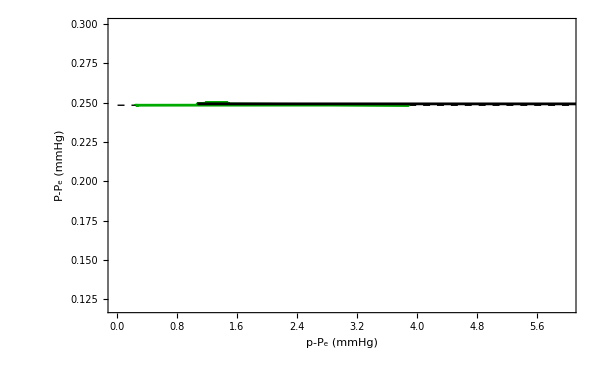

```mathematica
(*(*--- 2.a Phase diagram: P-Subscript[P, e] vs p-Subscript[P, e] ---*)
(*--- Correct sorting ---*)
(*pos=Part[Position[P1,Max[P1[[;;,2]]]],1,1];
aux1=Select[P1,Part[#,1]<P1[[pos,1]]&&Part[#,2]>1.005*(2(γM+ΤC)/r0) cf&];
aux1=Sort[aux1,#1[[2]]>#2[[2]]&]; 
aux2=DeleteDuplicates[#2~Join~#]~Drop~Length[#2]&[P1,aux1];
aux2=Sort[aux2,#1[[2]]<#2[[2]]&]; 
P1=Join[aux2,aux1];*)

range={{0,6},{0.12,0.3}};
f2a=Show[Plot[(2(γM+ΤC)/r0) cf,{x,p1,p2},PlotRange->All,PlotStyle->{Black,dashsty}],ListPlot[P3,PlotStyle->{DotDashed,mdefault}],
ListPlot[P1,PlotStyle->cdefault],
ListPlot[P2,PlotStyle->mdefault],
PlotRange->range,Frame->True,BaseStyle->bfont,FrameLabel->{Style["p-P_e (mmHg)",bfont],Style["P-P_e (mmHg)",bfont]},FrameStyle->{bfont,bfont},ImageSize->imgSize,ImagePadding->imagePadding]
fname2a=StringJoin["inset_",ToString[indx],".pdf"];
Export[fname2a,f2a];*)
```